### Introduction

Linear optimization is also known as linear programming (LP).

Linear optimization is a convex optimization problem that can be solved globally and efficiently.

Linear optimization finds x∈ℝ^n that solves the primal problem: »

| minimize | c.x
       | subject to constraints | a.x+b\[VectorGreaterEqual]0,
a_eq.x+b_eq=0
       | where | c∈ℝ^n,a∈ℝ^(m×n),b∈ℝ^m,a_eq∈ℝ^(k×n),b_eq∈ℝ^k

### Basic Example

Let’s start by defining our linear objective function:

```mathematica
objective[x_,y_] := 3x-5y
```

We can visualize the objective function  through its contour plot:

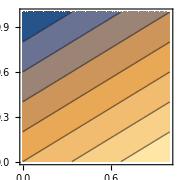

```mathematica
ContourPlot[objective[x,y],{x,0,1},{y,0,1},ImageSize->Small]
```

Then, we define a set of inequality constrains:

```mathematica
ineqConstraints[x_,y_]:= And @@{x≥ .15 ,y ≥ .15 , 2x + y ≤ 2,x + 3y ≤ 3}
eqConstraints[x_,y_] := x+y==1
```

We can also visualize the region it defines:

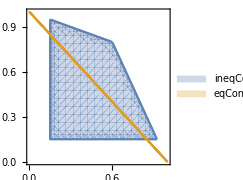

```mathematica
RegionPlot[{ineqConstraints[x,y],eqConstraints[x,y]},{x,0,1},{y,0,1},ImageSize->Small,PlotLegends->"Expressions"]
```

The function LinearOptimization is used to solve  the LP problem:

```mathematica
sol = LinearOptimization[objective[x,y],ineqConstraints[x,y]&& eqConstraints[x,y],{x,y}]
```

{x→0.15,y→0.85}

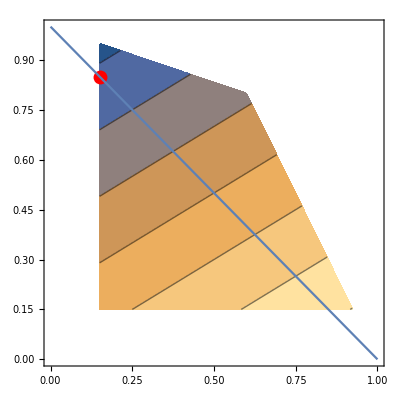

```mathematica
Show[
ContourPlot[{objective[x,y]},{x,0,1},{y,0,1},RegionFunction->Function[{x,y},ineqConstraints[x,y]]],
Graphics[{PointSize[.025],Red, Point[{x,y} /. sol] }],
ContourPlot[Evaluate[eqConstraints[x,y]],{x,0,1},{y,0,1}]]
```

### Standard Matrix Form

| minimize | c.x
       | subject to constraints | a.x+b\[VectorGreaterEqual]0,
a_eq.x+b_eq=0
       | where | c∈ℝ^n,a∈ℝ^(m×n),b∈ℝ^m,a_eq∈ℝ^(k×n),b_eq∈ℝ^k

```mathematica
objective[x_,y_] := 3x-5y
```

we can extract c as

```mathematica
c = {3,-5};
```

Inequality Constraints:

```mathematica
ineqConstraints[x_,y_]:= And @@{x≥ .15 ,y ≥ .15 , 2x + y ≤ 2,x + 3y ≤ 3}
eqConstraints[x_,y_] := x+y==1
```

```mathematica
A = {{1,0},{0,1},{-2,-1},{-1,-3}};
b= {-0.15,-0.15,2,3};
```

```mathematica
Row[{MatrixForm[A],MatrixForm[{x,y}],"+",MatrixForm[b],"\[VectorGreaterEqual]",MatrixForm[Table[0,Length[b]]] }]
```

(1 | 0
0 | 1
-2 | -1
-1 | -3)(x
y)+(-0.15
-0.15
2
3)\[VectorGreaterEqual](0
0
0
0)

Inequality Constraints:

```mathematica
Aeq = {{1,1}};
beq = {-1};
```

```mathematica
Row[{MatrixForm[Aeq],MatrixForm[{x,y}],"+",MatrixForm[beq],"=",MatrixForm[Table[0,1]] }]
```

(1 | 1)(x
y)+(-1)=(0)

Solve:

```mathematica
LinearOptimization[c,{A,b},{Aeq,beq}]
```

{0.15,0.85}